```mathematica
a-Graphics-
```

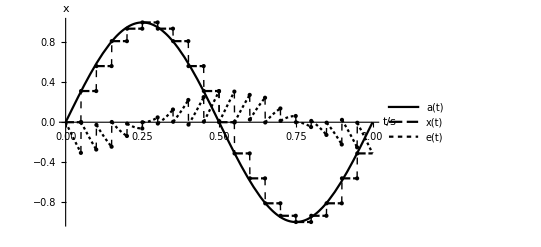

```mathematica
Ts=0.05;δ=0.0625;
a[t_]:=Sin[2 π t];
x[t_]:=Round[Sin[2 π Floor[t/Ts] Ts]/δ] δ;
e[t_]:=x[t]-a[t];
Plot[{a[t],x[t],e[t]},{t,0,1},PlotLegends->{"a(t)","x(t)","e(t)"},ExclusionsStyle->{Dashed,Dotted},PlotTheme->"Monochrome",AxesLabel->{"t/s","x"}]
```

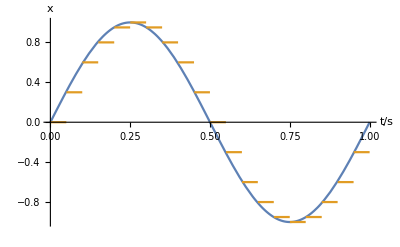

```mathematica
Show[%147,AxesLabel->{HoldForm["t/s"],HoldForm[x]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%148,PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

-Graphics-

```mathematica
Show[%149,AxesStyle->Black]
```

-Graphics-